# qubit rotations

P. Huft

The math here generalizes to other qubit platforms, but for concreteness I’ll use the language of lasers or microwaves manipulating atomic qubits.

## functions - run first

```mathematica
BuildMasterEq[ρ0_,H_]:=Module[{dim,rho,eqIdcs,comm,linblad,rhoPruned,eqsPruned,rhoICPruned, popIdxList, cohIdxList},
(*The junk below just builds the eqs to be passed to NDSolve, removing the redundant matrix elements. The derivatives could be worked out explicitly and typed in (just the optical Bloch equations) but this can the heavy lifting for higher than 2-dimensional systems.

"Pruned" variables refer to the eqs which have had the redundant element removed

Args: ρ0, the initial density matrix; H, the Hamiltonian
Returns: eqsPruned, rhoICPruned (the pruned initial state), rhoPruned (the pruned set of variables, i.e. elements of ρ, to solve for), popIdxList (the indices of the population terms), cohIdxList (inds of the coherence terms)
*)
Clear[ρ,t];
dim = Length[H];
rho=Array[Subscript[ρ, #1,#2][t](*[#1,#2][t]*)&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm = rho.H - H.rho ;
(*linblad =Γ(σm.rho.σp-1/2((σp.σm).rho + rho.(σp.σm)));*)
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==-ⅈ comm[[i,j]]];(*+linblad[[i,j]]];*)
AppendTo[rhoICPruned,(rho/.t-> 0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]]
]
]
]
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems,i++
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
];
{eqsPruned,rhoICPruned,rhoPruned, popIdxList, cohIdxList}
];

(*graphic for creating a state vector on the Bloch sphere*)
BlochSphereVector[θ_,ϕ_]:=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},{Red,Thick,Arrow[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],-Cos[θ]}}]},{Blue,Thick,Dashed,Line[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],0}}]},
{Blue,Thick,Dashed,Line[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],-Cos[θ]}}]},{Green,Thick,Dashed,Line[{{0,0,0},{0,0,-Cos[θ]}}]},
{Green,Thick,Dashed,Line[{{0,0,-Cos[θ]},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],-Cos[θ]}}]},Text[Style["0",20],{0,0,1.3}],Text[Style["1",20],{0,0,-1.3}],Text[Style["X",20],{1.3,0,0}],Text[Style["Y",20],{0,1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Medium];

SingleQubitRhoPlot[ϕ_,ρ00_,ρ01_,ρ11_]:=Module[{z,opacity=0.75,cf},
cf[x_]:=Blend[{Blue,Green,Yellow,Red,Blue},(x+2π)/(4π)];
SquareBar[xmin_,ymin_,width_,zmin_,zmax_]:=Cuboid[{xmin,ymin,zmin},{xmin+width,ymin+width,zmax}];
Legended[Graphics3D[{{Opacity[opacity],Blue,SquareBar[0,0,0.9,0,z]}/.z-> ρ00,
{Opacity[opacity],cf[ϕ],SquareBar[0,1,0.9,0,z]}/.z-> Abs[ρ01],
{Opacity[opacity],cf[-ϕ],SquareBar[1,0,0.9,0,z]}/.z-> Abs[ρ01],
{Opacity[opacity],Blue,SquareBar[1,1,0.9,0,z]}/.z-> ρ11,Text[Style["0",20],{0.5,-0.3,0}],Text[Style["1",20],{1.5,-0.3,0}],Text[Style["0",20],{2.3,0.5,0}],Text[Style["1",20],{2.3,1.5,0}]},BoxRatios->{2,2,1.5},ImageSize->Medium,Axes->{False,False,True},AxesLabel->{"","",Text[Style["|ρ_(i, j)|",20,Black]]},Ticks-> {{},{},{0,0.25,0.5,0.75,1}},PlotRange->{{-.3,2.3},{-.3,2.3},{0,1}}],BarLegend[{cf[#]&,{-2π,2π}},LegendLabel->"ϕ [rad]" ]]
];

(*convenience operators for grabbing the two qubit elements out of the solution*)
ρ00[soln_]:=soln[[1,2]];
ρ01[soln_]:=soln[[2,2]];
ρ11[soln_]:=soln[[3,2]];
(*qubit angle operators*)
theta[soln_]:=2ArcTan[soln//ρ11, soln//ρ00];
phi[soln_]:=Arg[(soln//ρ01)/Abs[soln//ρ01]];
```

## single qubit gates

### Rabi oscillations - resonant

Population transfer between 0 and 1 by applying a constant laser or microwave pulse on resonant with the qubit transition. It is clear from looking at the Bloch vector that the Hamiltonian is performing a rotation about the X axis. When the rotation is through an angle π, this is called an X gate. This can also be seen just from looking at the Hamiltonian, which is proportional to the Pauli matrix σ_x.

```mathematica
(*initial qubit state*)
ρ0=({{1, 0}, {0, 0}});
(*build hamiltonian and symbolic ρ*)
Clear[Ω,Δ,Γ];
H = ({{0, Ω}, {Ω, -Δ}});(*Hamiltonian with the rotating wave approximation (RWA)*)
Ω =2π; (*Rabi frequency*)
Δ =0; (*qubit/laser detuning*)
Γ=0; (*decay rate*)
tmax = 1; (*evolution time*)
```

Time to run sim: 0.015625

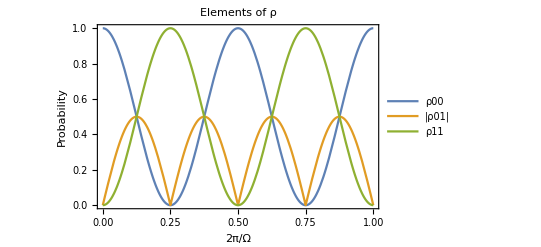

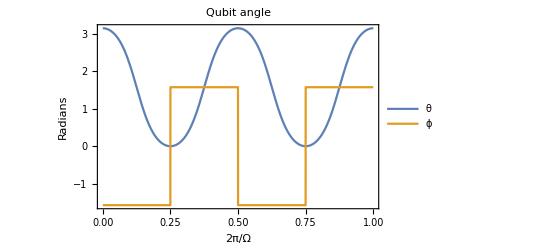

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*build the equations*)
{eqs,IC, rho,popIdxList,cohIdxList}=BuildMasterEq[ρ0,H];
(*solve for the time evolution*)
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,IC], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
(*build a plot of the elements*)
plt ={};
labels ={"ρ00","|ρ01|","ρ11"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,Abs[soln[[i,2]]]]
];

(*plot the populations and coherence*)
Plot[Evaluate[plt], {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Probability"},PlotLabel->"Elements of ρ"]
labels = {"θ","ϕ"};

(*plot the qubit angles*)
θ=soln//theta;
ϕ=soln//phi;

Plot[{θ,ϕ},{t,0,tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Radians"},PlotLabel->"Qubit angle"]

(*show the vector on the Bloch sphere with a manipulate plot*)
(*Manipulate[BlochSphereVector[θ,ϕ]/.t-> τ,{τ,0.001,1}]*)
Manipulate[GridBox[{{BlochSphereVector[θ,ϕ]/.t-> τ,Quiet[SingleQubitRhoPlot@@Table[soln//op,{op,{phi,ρ00,ρ01,ρ11}}]/.t->τ]}}]//DisplayForm,{τ,0.001,1,0.001} ]
```

### Rabi oscillations - constant detuning

Population transfer between 0 and 1 by applying a constant laser or microwave pulse off resonant with the qubit transition. The oscillations are faster than the resonant case and the population transfer is incomplete, which is a good diagnostic for laser frequency in the lab. The incomplete rotation is not very obvious for small detuning, so it is helpful to generate plots below with large detuning (of order or greater than the Rabi frequency).

```mathematica
(*initial qubit state*)
ρ0=({{1, 0}, {0, 0}});
(*build hamiltonian and symbolic ρ*)
Clear[Ω,Δ,Γ];
H = ({{0, Ω}, {Ω, -Δ}});(*Hamiltonian with the rotating wave approximation (RWA)*)
Ω =2π; (*Rabi frequency*)
Δ =Ω; (*qubit/laser detuning*)
Γ=0; (*decay rate*)
tmax = 1; (*evolution time*)
```

Time to run sim: 0.

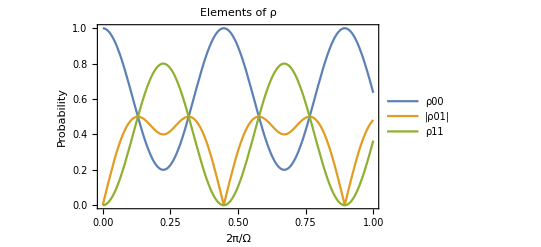

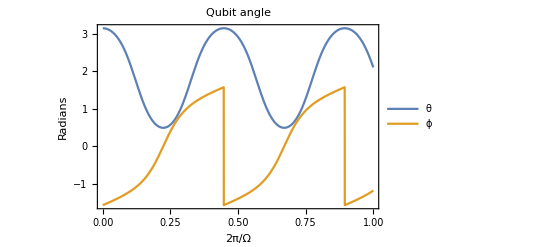

```mathematica
(*build the equations*)
{eqs,IC, rho,popIdxList,cohIdxList}=BuildMasterEq[ρ0,H];
(*solve for the time evolution*)
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,IC], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
(*build a plot of the elements*)
plt ={};
labels ={"ρ00","|ρ01|","ρ11"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,Abs[soln[[i,2]]]]
];

(*plot the populations and coherence*)
Plot[Evaluate[plt], {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Probability"},PlotLabel->"Elements of ρ"]
labels = {"θ","ϕ"};

(*plot the qubit angles*)
θ=soln//theta;
ϕ=soln//phi;

Plot[{θ,ϕ},{t,0,tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Radians"},PlotLabel->"Qubit angle"]

(*show the vector on the Bloch sphere with a manipulate plot*)
(*Manipulate[BlochSphereVector[θ,ϕ]/.t-> τ,{τ,0.001,1}]*)
Manipulate[GridBox[{{BlochSphereVector[θ,ϕ]/.t-> τ,Quiet[SingleQubitRhoPlot@@Table[soln//op,{op,{phi,ρ00,ρ01,ρ11}}]/.t->τ]}}]//DisplayForm,{τ,0.001,1,0.001} ]
```

### Adiabatic Rapid Passage (ARP)

By sweeping the frequency of the laser or microwaves through the qubit resonance, we can drive a transition adiabatically. This occurs when the detuning at the beginning and end of the sweep is much greater than the Rabi frequency, so essentially no population transfer occurs at those times. The population is transferred rapidly as the detuning goes through zero. Note the small oscillations at the tails of the sweep: these are at the frequency of the detuning we are in a frame rotating with the qubit.

```mathematica
(*initial qubit state*)
ρ0=({{1, 0}, {0, 0}});
(*build hamiltonian and symbolic ρ*)
Clear[Ω,Δ,Γ];
H = ({{0, Ω}, {Ω, -Δ}});(*Hamiltonian with the rotating wave approximation (RWA)*)
Ω =2π; (*Rabi frequency*)
Δ =10Ω(1-t/(tmax/2)); (*qubit/laser detuning*)
Γ=0; (*decay rate*)
tmax = 5; (*evolution time*)
```

Time to run sim: 0.

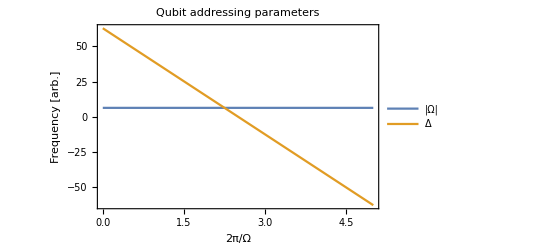

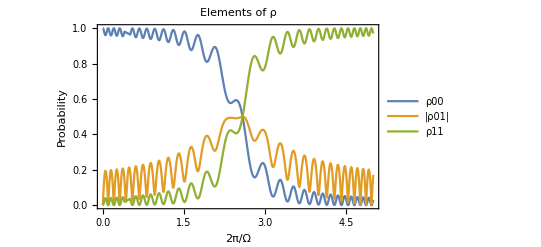

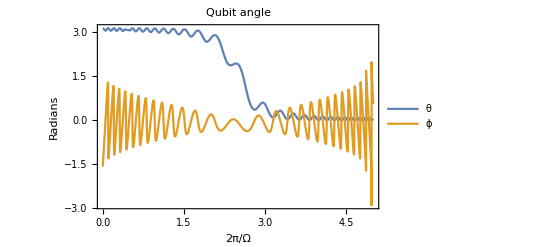

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*build the equations*)
{eqs,IC, rho,popIdxList,cohIdxList}=BuildMasterEq[ρ0,H];
(*solve for the time evolution*)
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,IC], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
(*build a plot of the elements*)
plt ={};
labels ={"ρ00","|ρ01|","ρ11"};
For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,Abs[soln[[i,2]]]]
];

(*plot the Rabi frequency and detuning*)
labels = {"|Ω|","Δ"};
Plot[{Abs[Ω],Δ}, {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Frequency [arb.]"},PlotLabel->"Qubit addressing parameters"]


(*plot the populations and coherence*)
labels ={"ρ00","|ρ01|","ρ11"};
Plot[Evaluate[plt], {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Probability"},PlotLabel->"Elements of ρ"]

(*plot the qubit angles*)
θ=soln//theta;
ϕ=soln//phi;
labels = {"θ","ϕ"};
Plot[{θ,ϕ},{t,0,tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Radians"},PlotLabel->"Qubit angle"]

(*show the vector on the Bloch sphere with a manipulate plot*)
(*Manipulate[BlochSphereVector[θ,ϕ]/.t-> τ,{τ,0.001,1}]*)
Manipulate[GridBox[{{BlochSphereVector[θ,ϕ]/.t-> τ,Quiet[SingleQubitRhoPlot@@Table[soln//op,{op,{phi,ρ00,ρ01,ρ11}}]/.t->τ]}}]//DisplayForm,{τ,0.01,tmax,0.001}]
```

### Time-dependent Rabi frequency

Ramping the microwave power (i.e. the Rabi freq.).

One way of doing a rapid X gate is by simply applying a very short but high power Rabi pulse such that the integral of the pulse is still π. For a Gaussian pulse Ω_peak Exp[-a t^2], the time integral is Ω_peak √(π/a), so we want a=Ω_peak^2/π. For tmax=10, Ω =2 π Exp[-50(t-tmax/2)^2] approximately satisfies this.

```mathematica
(*initial qubit state*)
ρ0=({{1, 0}, {0, 0}});
(*build hamiltonian and symbolic ρ*)
Clear[Ω,Δ,Γ];
H = ({{0, Ω}, {Ω, -Δ}});(*Hamiltonian with the rotating wave approximation (RWA)*)
Ω =2 π Exp[-50(t-tmax/2)^2]; (*Rabi frequency*)
Δ =0; (*qubit/laser detuning*)
Γ=0; (*decay rate*)
tmax = 10; (*evolution time*)
```

Time to run sim: 0.

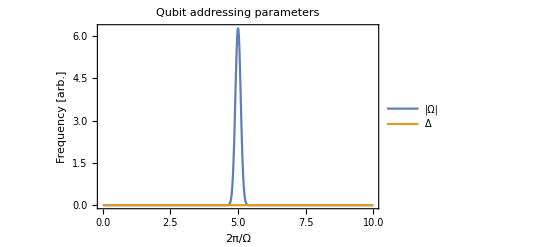

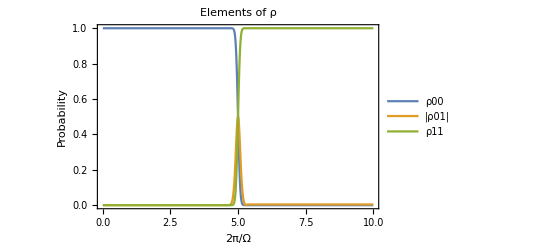

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

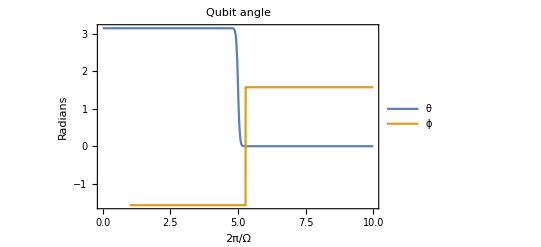

```mathematica
(*build the equations*)
{eqs,IC, rho,popIdxList,cohIdxList}=BuildMasterEq[ρ0,H];
(*solve for the time evolution*)
{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,IC], rho, {t,0,tmax}]];
Print["Time to run sim: ",time];
(*build a plot of the ρ elements*)
plt ={};

For[i=1, i<Length[soln]+1,i++,
AppendTo[plt,Abs[soln[[i,2]]]]
];

(*plot the Rabi frequency and detuning*)
labels = {"|Ω|","Δ"};
Plot[{Ω,Δ}, {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Frequency [arb.]"},PlotLabel->"Qubit addressing parameters"]


(*plot the populations and coherence*)
labels ={"ρ00","|ρ01|","ρ11"};
Plot[Evaluate[plt], {t, 0, tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Probability"},PlotLabel->"Elements of ρ"]

(*plot the qubit angles*)
θ=soln//theta;
ϕ=soln//phi;
labels = {"θ","ϕ"};
Plot[{θ,ϕ},{t,0,tmax},PlotRange->All,PlotLegends->labels,Axes-> Off,Frame-> {True,True,False,False},FrameLabel-> {"2π/Ω","Radians"},PlotLabel->"Qubit angle"]

(*show the vector on the Bloch sphere with a manipulate plot*)
(*Manipulate[BlochSphereVector[θ,ϕ]/.t-> τ,{τ,0.001,1}]*)
Manipulate[GridBox[{{BlochSphereVector[θ,ϕ]/.t-> τ,Quiet[SingleQubitRhoPlot@@Table[soln//op,{op,{phi,ρ00,ρ01,ρ11}}]/.t->τ]}}]//DisplayForm,{τ,0.01,tmax,0.001}]
```